### Parameter definitions

```mathematica
d=1;
λ=0.15;
q=0.6;
```

### Differential equations

```mathematica
dS1[t_] =   Cross[1/(2 d^3)((4+3/q-3/(q+1)λ)J[t]-S1[t]),S1[t]];
dS2[t_] =    Cross[1/(2 d^3)((4+3q-(3q)/(q+1)λ)J[t]-S2[t]),S2[t]];
dJ[t_]=     {0,0,0}  ;
```

### Numerical solution

```mathematica
sol=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]=={0.001,0,0.001},S2[0]=={0.005,0,0.001}, J[0]=={0,0,10}   },   {S1,S2,J},{t,0,30}];
```

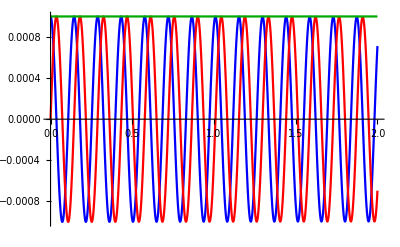

```mathematica
output[t_]:= (S1/.sol[[1]])[t];
Plot[{output[t][[1]],output[t][[2]],output[t][[3]]}, {t,0,2},PlotStyle->{Blue,Red,Darker[Green]}]
```

#### Vector definitions with numerical solution

```mathematica
S1v[t_]:=(S1/.sol[[1]])[t];
S2v[t_]:=(S2/.sol[[1]])[t];
Jv[t_]:=(J/.sol[[1]])[t];
Lv[t_]:=Jv[t]-S1v[t]-S2v[t];
Sv[t_]:=S1v[t]+S2v[t];
```

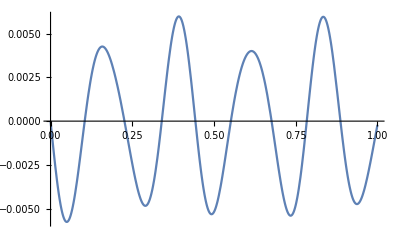

```mathematica
Plot[Lv[t][[2]],{t,0,1}]
```

#### Vector modulus

```mathematica
NormS1[t_]:=Norm[S1v[t]];
NormS2[t_]:=Norm[S2v[t]];
NormJ[t_]:=Norm[Jv[t]];
NormL[t_]:=Norm[Lv[t]];
NormS[t_]:=Norm[Sv[t]];
```

#### Unit vector definitions

```mathematica
S1u[t_]:=S1v[t]/NormS1[t];
Su[t_]:=Sv[t]/NormS[t];
```

#### Definitions of θ_L

```mathematica
cosθL[t_]:=(NormJ[t]^2+NormL[t]^2-NormS[t]^2)/(2NormJ[t]NormL[t]);
```

```mathematica
sinθL[t_]:=cosθL[N[π/2]-t];
```

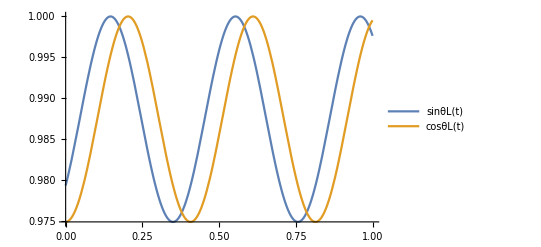

```mathematica
Plot[{sinθL[t],cosθL[t]},{t,0,1},PlotRange->All, PlotLegends->"Expressions"]
```

#### Orthogonal vector definition

```mathematica
SO[t_]:={(NormJ[t]-NormL[t]cosθL[t])/NormS[t],0,(NormL[t]sinθL[t])/NormS[t]};
```

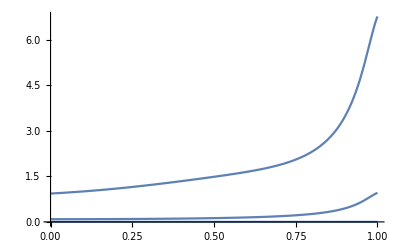

```mathematica
Plot[SO[t],{t,0,1},PlotRange->All]
```

#### Angle ϕ’ definitions

```mathematica
DotProduct1[t_]:=Dot[S1u[t],SO[t]];
```

```mathematica
CrossProduct1[t_]:=Cross[S1u[t],Su[t]];
```

```mathematica
NormCross1[t_]:=Norm[CrossProduct1[t]];
```

```mathematica
cosϕ[t_]:=DotProduct1[t]/NormCross1[t];
```

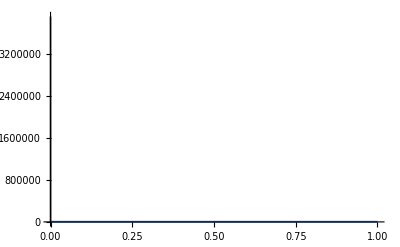

```mathematica
Plot[cosϕ[t],{t,0,1},PlotRange->All]
```